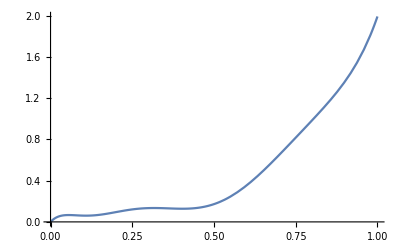

1.99289

2.84217×10^-13

```mathematica
Clear["Global`*"]

Lx=3.25;
Ly=11;
bactDiff=0.2;
substrDiff = 0.2;

g[s_]:=1.99289 -9.17449*(1-s) + 40.0716*(1-s)^2 -143.678*(1-s)^3+325.762*(1-s)^4-679.34*(1-s)^5+1451.89*(1-s)^6-2072.97*(1-s)^7+1519.2*(1-s)^8-433.754*(1-s)^9;


Plot[g[x],{x,0,1}]
g[1]
g[0]
```

```mathematica
(* Coupled bacteria and nutrient fields in 2D *)
```

```mathematica
tend=20
soln=NDSolve[{
(* Equations *)
D[n[x,y,t],t]-bactDiff*(D[n[x,y,t],{x,2}]+D[n[x,y,t],{y,2}])- n[x,y,t]*g[s[x,y,t]]==0,
D[s[x,y,t],t]-substrDiff*(D[s[x,y,t],{x,2}]+D[s[x,y,t],{y,2}])+ n[x,y,t]*g[s[x,y,t]]==0,
(* -- ICs -- *)
(*n[x,y,0]==Piecewise[{{0.05,(x-1.2)^2+(y-5)^2<0.8}},0],*)
(*n[x,y,0]==Piecewise[{{0.05,1.3<x<2.0&&4<y<5}},0],*)
(*n[x,y,0]==0.9*UnitBox[x-2,y-2],*)
(*n[x,y,0]==0.00006*(x y)^2*(Lx-x)^2*(Ly-y)^2*Exp[  -2*( (x-0.5*Lx)^2  +  (y-0.8*Ly)^2/4   )  ],*)
n[x,y,0]==0.000000001*(x*y)^2*(Lx-x)^2*(Ly-y^2)^2,
(*n[x,y,0]==0.00005*(x y)^2*(Lx-x)^2*(Ly-y)^2,*)
(*s[x,y,0]== 0.75+0.05*Sin[(x*y)],*)
(*s[x,y,0]==0.95*Exp[  -1*( (x-L/2)^2/(2*15^2)  +  (y-L/2)^2/(2*15^2)   )  ],*)
s[x,y,0]==0.95,
(* -- BCs -- *)
Derivative[1,0,0][n][Lx,y,t]==0,Derivative[1,0,0][n][0,y,t]==0,Derivative[0,1,0][n][x,Ly,t]==0,Derivative[0,1,0][n][x,0,t]==0,
Derivative[1,0,0][s][Lx,y,t]==0,Derivative[1,0,0][s][0,y,t]==0,Derivative[0,1,0][s][x,Ly,t]==0,Derivative[0,1,0][s][x,0,t]==0},
  {n,s},{t,0,tend},{x,0,Lx},{y,0,Ly}]
(*{n,s},{t,0,tend},{x,0,Lx},{y,0,Ly},Method->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", MaxPoints->500}}]*)
```

20

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{n→InterpolatingFunction[{{0., 3.25}, {0., 11.}, {0., 20.}}, <>],s→InterpolatingFunction[{{0., 3.25}, {0., 11.}, {0., 20.}}, <>]}}

```mathematica
(*Plot3D[n[x,y,t]/.please[[1]]/.{t-> 0},{x,0,L},{y,0,L},PlotRange->{0,1.1},AxesLabel->Automatic]*) 
(*Plot3D[s[x,y,t]/.please[[1]]/.{t-> 0},{x,0,L},{y,0,L},PlotRange->{0,1.1},AxesLabel->Automatic]*)
tplot =11
Plot3D[{n[x,y,t]/.soln[[1]]/.{t-> tplot}, s[x,y,t]/.soln[[1]]/.{t-> tplot}},{x,0,Lx},{y,0,Ly},PlotRange->{-0.1,1.1},AxesLabel->Automatic]
```

11

-Graphics3D-

```mathematica
(* Animate[Plot3D[{n[x,y,t]/.soln[[1]]/.{t-> ttt}, s[x,y,t]/.soln[[1]]/.{t-> ttt}},{x,0,L},{y,0,L},PlotRange->{-0.1,1},AxesLabel->Automatic],{ttt,0,10}] *)
```

```mathematica
(* Why does the dt increment here change the axis values!? *)
```

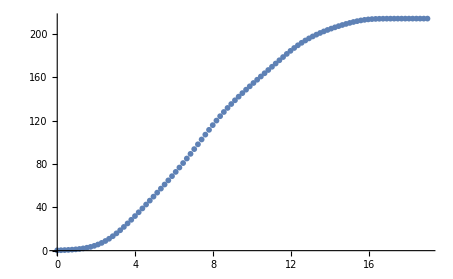

```mathematica
ListPlot[Table[Sum[n[x,y,t]/.soln[[1]]/.{t->dt}, {x,Lx/2-0.5,Lx/2+0.5,0.25},{y,0,Ly,0.25}],{dt,0,20,0.2}],DataRange->{0,19}]
```

```mathematica
cc=Cases[-Graphics-,x_Point:>First@x,Infinity]
```

{{{0.,0.293687},{0.19,0.400366},{0.38,0.527882},{0.57,0.693198},{0.76,0.910524},{0.95,1.19539},{1.14,1.56848},{1.33,2.05234},{1.52,2.67247},{1.71,3.46008},{1.9,4.44806},{2.09,5.66627},{2.28,7.14703},{2.47,8.9144},{2.66,10.9782},{2.85,13.3345},{3.04,15.9629},{3.23,18.8314},{3.42,21.9002},{3.61,25.1271},{3.8,28.4716},{3.99,31.9105},{4.18,35.4163},{4.37,38.9724},{4.56,42.569},{4.75,46.198},{4.94,49.8579},{5.13,53.5495},{5.32,57.2767},{5.51,61.0457},{5.7,64.8642},{5.89,68.7422},{6.08,72.6907},{6.27,76.7195},{6.46,80.8372},{6.65,85.0487},{6.84,89.3488},{7.03,93.7253},{7.22,98.1593},{7.41,102.625},{7.6,107.091},{7.79,111.514},{7.98,115.848},{8.17,120.052},{8.36,124.105},{8.55,127.999},{8.74,131.737},{8.93,135.331},{9.12,138.796},{9.31,142.149},{9.5,145.405},{9.69,148.581},{9.88,151.692},{10.07,154.75},{10.26,157.771},{10.45,160.767},{10.64,163.751},{10.83,166.736},{11.02,169.728},{11.21,172.729},{11.4,175.731},{11.59,178.706},{11.78,181.619},{11.97,184.423},{12.16,187.078},{12.35,189.559},{12.54,191.858},{12.73,193.98},{12.92,195.935},{13.11,197.737},{13.3,199.402},{13.49,200.944},{13.68,202.376},{13.87,203.714},{14.06,204.965},{14.25,206.142},{14.44,207.252},{14.63,208.3},{14.82,209.29},{15.01,210.219},{15.2,211.078},{15.39,211.85},{15.58,212.512},{15.77,213.052},{15.96,213.462},{16.15,213.748},{16.34,213.93},{16.53,214.039},{16.72,214.101},{16.91,214.136},{17.1,214.156},{17.29,214.168},{17.48,214.176},{17.67,214.181},{17.86,214.185},{18.05,214.188},{18.24,214.191},{18.43,214.194},{18.62,214.197},{18.81,214.194},{19.,214.209}}}

```mathematica
{{{0.,2.936868455493183},{1.,9.456092893946968},{2.,21.671118655988828},{3.,37.348148428748075},{4.,54.41221729282092},{5.,72.77797412048163},{6.,93.57072660172585},{7.,116.31033234626665},{8.,136.61727552252242},{9.,153.27317844249473},{10.,168.66818743417227},{11.,183.32674731385814},{12.,195.3139712880519},{13.,204.03896102788903},{14.,210.3286661930171},{15.,215.07126946590415},{16.,217.46385082117402},{17.,217.86673117070086},{18.,218.00970390328314},{19.,218.11914141620264}}}

Export["plot_PDEs2.dat",cc[[1]]]
```

{{{0.,2.93687},{1.,9.45609},{2.,21.6711},{3.,37.3481},{4.,54.4122},{5.,72.778},{6.,93.5707},{7.,116.31},{8.,136.617},{9.,153.273},{10.,168.668},{11.,183.327},{12.,195.314},{13.,204.039},{14.,210.329},{15.,215.071},{16.,217.464},{17.,217.867},{18.,218.01},{19.,218.119}}}

plot_PDEs2.dat

{{nn[t]→InterpolatingFunction[{{0., 20.}}, <>][t],ss[t]→InterpolatingFunction[{{0., 20.}}, <>][t]}}

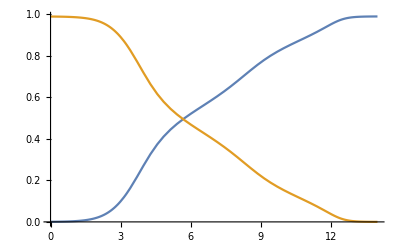

```mathematica
(*   WELL MIXED EQUATIONS   *)
solnsWM=NDSolve[{nn'[t]==nn[t]*g[ss[t]],ss'[t]==-nn[t]*g[ss[t]],nn[0]==0.0005,ss[0]==0.99},{nn[t],ss[t]},{t,0,20}]
Plot[{nn[t]/.solnsWM[[1]],ss[t]/.solnsWM[[1]]},{t,0,14}]
```

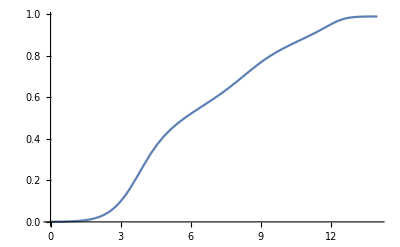

```mathematica
Plot[nn[t]/.solnsWM[[1]],{t,0,14}]
```

```mathematica
ccc=Cases[-Graphics-,x_Line:>First@x,Infinity]
```

{{{2.85714×10^-7,0.0005},{0.00429405,0.000504115},{0.00858782,0.000508255},{0.0171753,0.00051664},{0.0343504,0.000533824},{0.0687005,0.000569924},{0.0729943,0.000574605},{0.0772881,0.000579323},{0.0858756,0.000588875},{0.103051,0.000608449},{0.137401,0.000649565},{0.141695,0.000654896},{0.145988,0.000660271},{0.154576,0.000671154},{0.171751,0.00069346},{0.206101,0.000740312},{0.274801,0.00084369},{0.279456,0.000851193},{0.284111,0.000858764},{0.293421,0.000874106},{0.312041,0.000905615},{0.34928,0.000972059},{0.353935,0.000980699},{0.35859,0.000989415},{0.3679,0.00100708},{0.38652,0.00104336},{0.423759,0.00111986},{0.428414,0.00112981},{0.433069,0.00113984},{0.442379,0.00116018},{0.460999,0.00120194},{0.498238,0.00129001},{0.572717,0.00148584},{0.577063,0.00149814},{0.58141,0.00151054},{0.590103,0.00153565},{0.607489,0.00158712},{0.64226,0.00169525},{0.646607,0.00170927},{0.650953,0.0017234},{0.659646,0.00175202},{0.677032,0.00181068},{0.711804,0.00193392},{0.71615,0.00194989},{0.720497,0.001966},{0.729189,0.00199862},{0.746575,0.00206546},{0.781347,0.00220585},{0.85089,0.00251563},{0.855152,0.00253595},{0.859413,0.00255643},{0.867935,0.00259789},{0.88498,0.00268281},{0.91907,0.00286096},{0.923331,0.00288403},{0.927592,0.00290729},{0.936114,0.00295437},{0.953159,0.0030508},{0.987249,0.00325305},{0.99151,0.00327924},{0.995771,0.00330564},{1.00429,0.00335907},{1.02134,0.00346849},{1.05543,0.00369799},{1.12361,0.00420269},{1.12823,0.00423925},{1.13285,0.00427613},{1.1421,0.00435084},{1.16059,0.00450411},{1.19756,0.00482672},{1.20219,0.0048686},{1.20681,0.00491084},{1.21605,0.00499639},{1.23454,0.00517188},{1.27152,0.00554114},{1.27615,0.00558908},{1.28077,0.00563741},{1.29001,0.00573532},{1.3085,0.00593612},{1.34548,0.00635846},{1.41944,0.00729253},{1.42375,0.00735094},{1.42807,0.0074098},{1.43669,0.0075289},{1.45395,0.00777266},{1.48846,0.00828321},{1.49277,0.00834926},{1.49709,0.00841582},{1.50572,0.00855047},{1.52297,0.00882606},{1.55748,0.00940315},{1.5618,0.00947779},{1.56611,0.009553},{1.57474,0.00970514},{1.59199,0.0100164},{1.62651,0.0106678},{1.69553,0.0120937},{1.7002,0.0121966},{1.70488,0.0123003},{1.71423,0.0125102},{1.73293,0.0129402},{1.77033,0.0138425},{1.775,0.0139594},{1.77968,0.0140772},{1.78903,0.0143156},{1.80773,0.0148039},{1.84513,0.0158276},{1.8498,0.0159602},{1.85448,0.0160937},{1.86383,0.016364},{1.88253,0.0169172},{1.91993,0.0180762},{1.99473,0.0206175},{1.99932,0.0207836},{2.00391,0.020951},{2.01309,0.0212894},{2.03145,0.0219813},{2.06817,0.0234269},{2.14161,0.0265786},{2.14619,0.0267877},{2.15078,0.0269982},{2.15996,0.0274237},{2.17832,0.0282927},{2.21504,0.0301043},{2.28848,0.0340362},{2.29276,0.0342786},{2.29704,0.0345225},{2.3056,0.0350149},{2.32273,0.036018},{2.35698,0.0380985},{2.42548,0.0425684},{2.42976,0.0428619},{2.43404,0.043157},{2.44261,0.0437525},{2.45973,0.0449641},{2.49398,0.0474712},{2.56248,0.052831},{2.56713,0.0532113},{2.57177,0.0535939},{2.58105,0.0543657},{2.59962,0.0559361},{2.63676,0.0591855},{2.71104,0.0661298},{2.71569,0.0665839},{2.72033,0.0670404},{2.72961,0.0679607},{2.74818,0.0698301},{2.78532,0.0736859},{2.8596,0.0818721},{2.86394,0.0823695},{2.86827,0.082869},{2.87694,0.0838748},{2.89428,0.0859127},{2.92895,0.0900945},{2.99829,0.0988831},{3.13698,0.118158},{3.14123,0.118784},{3.14548,0.119412},{3.15398,0.120674},{3.17097,0.123223},{3.20496,0.128418},{3.27294,0.139191},{3.4089,0.162174},{3.70394,0.217186},{3.97923,0.271085},{4.27764,0.326538},{4.57059,0.374055},{4.8438,0.41142},{5.14012,0.445442},{5.4167,0.472577},{5.7164,0.498488},{6.01064,0.521657},{6.28513,0.542135},{6.58275,0.563882},{6.86061,0.584366},{7.13303,0.605098},{7.42855,0.628739},{7.70434,0.652109},{8.00324,0.678808},{8.29668,0.705912},{8.57038,0.731182},{8.8672,0.757523},{9.14427,0.780336},{9.41589,0.800686},{9.71062,0.820573},{9.98561,0.837397},{10.2837,0.854279},{10.5621,0.869304},{10.835,0.883851},{11.131,0.899979},{11.4073,0.915804},{11.7067,0.933971},{12.0006,0.952085},{12.0049,0.952341},{12.0092,0.952597},{12.0177,0.953108},{12.0349,0.954124},{12.0691,0.956131},{12.1377,0.96003},{12.142,0.960268},{12.1463,0.960505},{12.1548,0.960977},{12.172,0.961911},{12.2062,0.96374},{12.2748,0.967224},{12.2794,0.967451},{12.2841,0.967676},{12.2934,0.968124},{12.312,0.969005},{12.3491,0.970705},{12.3538,0.970912},{12.3584,0.971117},{12.3677,0.971524},{12.3863,0.972321},{12.4234,0.97385},{12.4281,0.974035},{12.4327,0.974218},{12.442,0.974581},{12.4606,0.97529},{12.4978,0.97664},{12.5721,0.979074},{12.5764,0.979205},{12.5808,0.979335},{12.5894,0.979592},{12.6068,0.980091},{12.6415,0.981034},{12.6458,0.981147},{12.6502,0.981259},{12.6588,0.981479},{12.6762,0.981907},{12.7109,0.982711},{12.7152,0.982807},{12.7196,0.982902},{12.7282,0.983089},{12.7456,0.983451},{12.7803,0.984129},{12.7846,0.98421},{12.7889,0.98429},{12.7976,0.984446},{12.815,0.98475},{12.8497,0.985316},{12.8539,0.985382},{12.8582,0.985447},{12.8667,0.985575},{12.8837,0.985822},{12.9177,0.986282},{12.9219,0.986337},{12.9262,0.986391},{12.9347,0.986497},{12.9517,0.986701},{12.9857,0.987081},{12.99,0.987126},{12.9942,0.98717},{13.0027,0.987257},{13.0197,0.987425},{13.0537,0.987737},{13.058,0.987773},{13.0623,0.98781},{13.0708,0.987881},{13.0878,0.988018},{13.1218,0.988272},{13.1264,0.988304},{13.131,0.988336},{13.1402,0.988399},{13.1587,0.988519},{13.1956,0.98874},{13.2002,0.988766},{13.2048,0.988792},{13.214,0.988841},{13.2325,0.988937},{13.2694,0.989113},{13.274,0.989133},{13.2786,0.989153},{13.2878,0.989193},{13.3063,0.989269},{13.3432,0.989408},{13.3478,0.989424},{13.3524,0.98944},{13.3616,0.989472},{13.3801,0.989532},{13.417,0.989641},{13.4213,0.989653},{13.4256,0.989665},{13.4342,0.989688},{13.4514,0.989733},{13.4859,0.989815},{13.4902,0.989824},{13.4945,0.989834},{13.5031,0.989852},{13.5203,0.989888},{13.5547,0.989953},{13.559,0.989961},{13.5633,0.989969},{13.572,0.989983},{13.5892,0.990012},{13.6236,0.990064},{13.6279,0.99007},{13.6322,0.990076},{13.6408,0.990088},{13.658,0.990111},{13.6925,0.990153},{13.6973,0.990158},{13.7021,0.990164},{13.7117,0.990174},{13.7309,0.990194},{13.7357,0.990199},{13.7405,0.990204},{13.7501,0.990213},{13.7694,0.990231},{13.7742,0.990235},{13.779,0.990239},{13.7886,0.990247},{13.8078,0.990263},{13.8462,0.990291},{13.851,0.990294},{13.8558,0.990298},{13.8655,0.990304},{13.8847,0.990316},{13.8895,0.990319},{13.8943,0.990322},{13.9039,0.990327},{13.9231,0.990338},{13.9279,0.990341},{13.9327,0.990343},{13.9423,0.990348},{13.9616,0.990357},{13.9664,0.99036},{13.9712,0.990362},{13.9808,0.990366},{13.9856,0.990368},{13.9904,0.99037},{13.9952,0.990372},{14.,0.990374}}}

```mathematica
Export["wellMixed3.dat",ccc[[1]]]
```

wellMixed3.dat